```mathematica
f[x_] = Log[x]
```

Log[x]

```mathematica
D[Log[x], x]
```

1/x

```mathematica
g[x_]=D[Log[x],x]
```

```mathematica
1/x
```

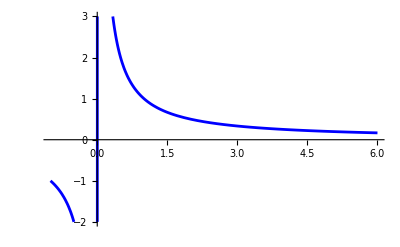

```mathematica
Plot[g[x],{x,-1,6}, PlotRange->{-2,3}, PlotStyle->Blue]
```

```mathematica
D[Log[x], x]
```

1/x

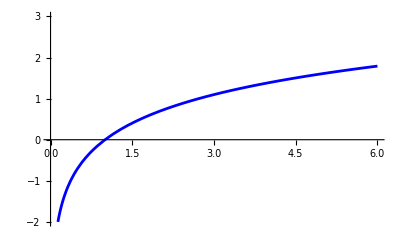

```mathematica
plot1 = Plot[f[x],{x,-1,6}, PlotRange -> {-2,3},PlotStyle ->Blue]
```

```mathematica
f[2]//N
```

0.693147

```mathematica
g[x_]=D[f[x],x]
```

ln

```mathematica
g[1]
```

ln

```mathematica
ln
```

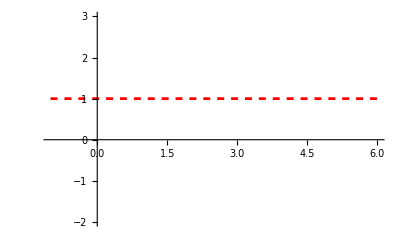

```mathematica
plot2 = Plot[,{x,-1,6}, PlotRange->{-2,3},PlotStyle-> {Dashed, Red}]
```

```mathematica
plot3 = Plot[1/E, {x,-1,6}, PlotRange->{-2,3}, PlotStyle -> {Dashed,Grey}]
```

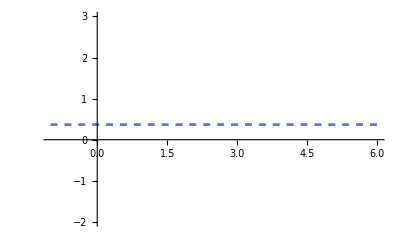

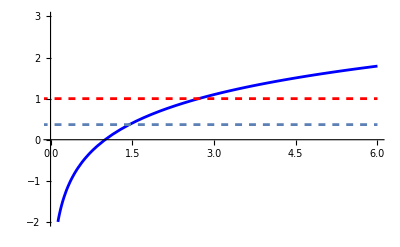

```mathematica
Show[plot1,plot2,plot3]
```

```mathematica
h[x_] = Piecewise[{{0,x<=0},{1,x>0}},{x,-2,2}]
```

Piecewise[{{0, x≤0}, {1, x>0}, {{x,-2,2}, True}}]

```mathematica
g[x_] =2h[x]-1
```

-1+2 (Piecewise[{{0, x≤0}, {1, x>0}, {{x,-2,2}, True}}])

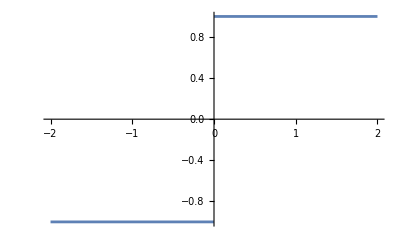

```mathematica
-1+2 (Piecewise[{{0, x≤0}, {1, x>0}, {{x,-2,2}, True}}])
Plot[g[x],{x,-2,2}]
```

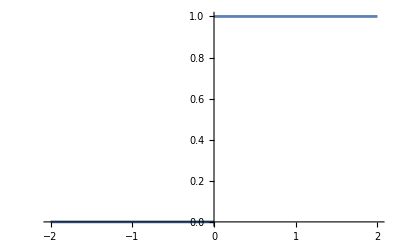

```mathematica
-1+2 (Piecewise[{{0, x≤0}, {1, x>0}, {{x,-2,2}, True}}]) (Piecewise[{{0, x_≤0}, {1, x_>0}, {{x_,-2,2}, True}}])
```

```mathematica
Plot[Piecewise[{{0,x<=0}, {1,x>0}}],{x,-2,2}]
```

-Graphics-